```mathematica
(*Clear all symbols from the Global context to start fresh*)
Clear["Global`*"];

(*Get the directory where the current notebook is located*)
currentDirectory=DirectoryName[NotebookFileName[]];

(*Create subfolders to save figures and data*)
folderfigures=FileNameJoin[{currentDirectory,"figures"}];
If[!DirectoryQ[folderfigures],CreateDirectory[folderfigures]];
folderdata=FileNameJoin[{currentDirectory,"data"}];
If[!DirectoryQ[folderdata],CreateDirectory[folderdata]];
folderdataIBM=FileNameJoin[{currentDirectory,"data_IBM/"}];
```

```mathematica
(*Define text styles for plots*)
style=Directive[FontFamily->"Arial",FontSize->18];
style2=Directive[FontFamily->"Arial",FontSize->24];

(*Define colors for plots*)
colorK=RGBColor["#004D80"];
Ngrey=RGBColor["#E6E6E6"];
colorφ = RGBColor["#5C3689"];
colorλ = RGBColor["#5B507A"];

colorIL=RGBColor["#EE4F70"];
colorSL = RGBColor["#48A8DF"];
colorF = RGBColor["#008080"];
```

```mathematica
(*Removes from the parameter `param` from the list of parameters `params`*)
DropParam[params_, param_]:=Drop[params,First[Position[Map[#[[1]]&, params], param]]]
(*Creates a list of replacement rules by pairing elements of `targets` and `subs`*)
MakeRule[targets_, subs_]:=Map[#[[1]]-> #[[2]]&, Transpose[{targets, subs}]]
```

```mathematica
(*Compute the probability l[a] of surving to age a.*)
Sl=DSolve[{l'[a]==-μ l[a],l[0]==1},l[a],a][[1]];

(*Average survival probability over the lifespan.*)
lm=Integrate[l[a]/.Sl,{a,0,1}];
Print["l[a]",l[a]/.Sl,", l̄ = ", lm]
```

l[a]ⅇ^(-a μ), l̄ = (1-ⅇ^-μ)/μ

## Preamble

### Demographic and cultural dynamics

```mathematica
(*Simulate coupled demographic and cultural dynamics until the age-specific knowledge and population distributions reach equilibrium.*)

GetResCultDemEq[listk0_,listn0_,Lu_,params_]:=Module[{na,da,dt,Index,dtOverDa,oneMinusDtOverDa,Lν,Ls,Lφ,Lsl,Lil,Lb,fiValues,fsValues,fbValues,kGrid,nGrid,kGridNew,nGridNew,A,P,Dens,Δ,i,n,eps,ia,φnum,iφ,kmin,kmax, r, kEx,nmin,nmax,nEx,ntilde,rsl,ril,neq,lN,OffspringByAge,R0,babyBorned,babyBuffer,nDelaySteps,ξN,ρN,γsN,γiN,γbN,eminN,emaxN,kdemiN,cN,μN,βN,αN ,ϵN,k0N,n0N,KN, fN, t0N,s0N,σN,MN
},

(*Extract parameters values*)
{ξN,ρN,γsN,γiN,γbN,eminN,emaxN,kdemiN,cN,μN,βN,αN ,ϵN,k0N,n0N,KN, fN, t0N, s0N,σN,MN}=N[{ξ,ρ,γs,γi,γb,emin,emax,kdemi,c,μ,β, α ,ϵ,k0,n0,K, f, t0, s0,σ,M}/. params];

(*Age grid setup*)
na=Length[Lu]; da=1/(na-1);dt=N[ 0.5 da] (*set the age and time step size*);
Index[a_]:=IntegerPart[a/da+1] (*Index maps a continuous age value to its integer grid index*);
dtOverDa=dt/da; oneMinusDtOverDa=1-dt/da (*Precompute weights used repeatedly in the age-transport updates.*);

(*Extract life-history strategy from Lu*)
{Lν,Ls,Lφ}=Developer`ToPackedArray/@N@Transpose[Lu];
{Lsl,Lil,Lb}={Lν*Ls,Lν*(1-Ls),1-Lν};
{fsValues,fiValues,fbValues}={Lsl^γsN,Lil^γiN,Lb^γbN};

(*Initialize knowledge and population grids*)
kGrid=Developer`ToPackedArray@N@listk0;nGrid=Developer`ToPackedArray@N@listn0;
kGridNew=ConstantArray[k0N,na];nGridNew=ConstantArray[n0N,na];

(*Probability to find a suitable exemplar at age a*)
A[a_,φ_,nEx_,ntilde_]:=ξN fN ⅇ^(-ρN (-a+φ)^2) nEx √(π /σN)/(fN+  ξN ntilde) ;

(*Instantaneous energy extraction rate*)
P[fb_,k_]:=fb (eminN+(emaxN-eminN)k/(kdemiN+k));

(*Density dependence population regulation*)
Dens[n_]=1/(1+ 0.1 n);

(*nDelaySteps:number of time steps corresponding to the juvenile delay t0,used to implement a discrete delay between birth and entry into the adult population. babyBuffer stores the history of birth events over this delay window.*)
nDelaySteps=Max[1,Round[t0N/dt]];
babyBuffer=ConstantArray[nGrid[[1]],nDelaySteps];

(*Iterative convergence loop for demographic–cultural dynamics*)
Δ=1;
i=0;
n=100000 (*Maximum number of iterations*);
eps=0.001 (*Convergence tolerance*);

While[Δ>eps dt && i<n,
Do[ia=Index[a];
(*Interpolate exemplar’s knowledge and density between ages*)
φnum=Clip[Lφ[[ia]],{0.,1.}];
iφ=Min[Floor[φnum/da]+1,na];
jφ=Min[iφ+1,na];

If[jφ==iφ,r=0.,r=(φnum-(iφ-1) da)/da];

kEx=(1-r) kGrid[[iφ]]+r kGrid[[jφ]];
nEx=(1-r) nGrid[[iφ]]+r nGrid[[jφ]];

(*Update population density over age*)
nGridNew[[ia]]=dtOverDa nGrid[[ia-1]] +oneMinusDtOverDa nGrid[[ia]] + dt (-μN nGrid[[ia]] );

(*Update knowledge for individuals of age a*)
ntilde=da Total[Table[nGrid[[iat]] ⅇ^(- ρN((iat-ia) da)^2),{iat,Range[2,na,1]}]];
rsl= βN A[a,φnum,nEx,ntilde] Max[kEx-kGrid[[ia]],0];
ril=αN (1-kGrid[[ia]]/KN);
kGridNew[[ia]]=dtOverDa kGrid[[ia-1]] +oneMinusDtOverDa kGrid[[ia]] +dt(fsValues[[ia]] rsl+fiValues[[ia]]ril-ϵN kGrid[[ia]] );

(*Boundary condition for newborn individuals (a=0)*)
If[a==da, 
kGridNew[[Index[0]]]=k0N;
nGridNew[[Index[0]]]=s0N babyBuffer[[1]];

neq=da Total[Table[nGridNew[[Index[at]]],{at,Range[da,1,da]}]];
babyBorned=da  cN Dens[neq]Total[Table[nGridNew[[iat]](P[fbValues[[iat]],kGridNew[[iat]]]-MN),{iat,Range[2,na,1]}]];
babyBuffer=Rest[Append[babyBuffer,babyBorned]];
] ,
{a,1,da,-da} (*loop over ages backwards*)
];

(*Compute convergence measure (Δ) for iteration stopping*)
Δ=0.5 Total[Abs[kGridNew-kGrid]]/Length[kGrid]+0.5 Total[Abs[nGridNew-nGrid]]/Length[nGrid];
i=i+1;

kGrid=Clip[kGridNew,{0,Infinity}];
nGrid=Clip[nGridNew,{0,Infinity}];
];

neq=da Total[Table[nGrid[[Index[at]]],{at,Range[da,1,da]}]];

If[i==n,Print["cultural and demographic dynamics: maximal numbers of iterations reached, Δ = ", Δ/dt," > ",eps,", Lu = " , Lu, ", kmax = ",Max[kGridNew]]];

(*Iterate over time t and age a to update knowledge values*)
lN[a_]=ⅇ^(-a μN);

OffspringByAge=Table[lN[a]P[fbValues[[ia]],kGrid[[Index[a]]]] cN Dens[neq],{a,Range[da,1,da]}];
R0=da Total[OffspringByAge];

(*Return the full knowledge grid*)
{neq,kGrid}
]
```

### Costate dynamics

```mathematica
(*Compute the age-specific costate of knowledge (λk) by solving the costate equation backward from the terminal age.*)

GetCostatekDyn[listk0_,listn0_,Lu_,params_]:=Module[{na,da,sol,Lν,Ls,Lφ,Lk,λkGrid,lN,lm,A, Index,P,dP,kcol,Pcomp,Pcop,neq, Dens,φnum,iφ,kmin,kmax,r,kEx,Lsl,Lil,Lb,fsValues,fiValues,fbValues,ia,ntilde,nExtilde,ξN,ρN,γsN,γiN,γbN,eminN,emaxN,kdemiN,cN,μN,βN,αN ,ϵN,k0N,n0N,KN, fN, t0N, s0N,σN,datak,kI
},

(*Extract parameters values*)
{ξN,ρN,γsN,γiN,γbN,eminN,emaxN,kdemiN,cN,μN,βN,αN ,ϵN,k0N,n0N,KN, fN, t0N, s0N,σN}=N[{ξ,ρ,γs,γi,γb,emin,emax,kdemi,c,μ,β, α ,ϵ,k0,n0,K, f, t0, s0,σ}/. params];

(*Age grid setup*)
na=Length[Lu]; da=1/(na-1)(*set the age step size*);
Index[a_]:=IntegerPart[a/da+1](*Index maps a continuous age value to its integer grid index*);

(*Extract trait components from Lu*)
{Lν,Ls,Lφ}=Developer`ToPackedArray/@N@Transpose[Lu];
{Lsl,Lil,Lb}={Lν*Ls,Lν*(1-Ls),1-Lν};
{fsValues,fiValues,fbValues}={Lsl^γsN,Lil^γiN,Lb^γbN};

(*Compute equilibrium knowledge values for each age and equilibrium population size*)
{neq,Lk}=GetResCultDemEq[listk0,listn0,Lu,params];


lN[a_]:=ⅇ^(-a μN) (*Probability of surving to age a*);
lm=N[(1-ⅇ^(- μN))/μN](*Average survival probability over the lifespan*);

(*Probability to find a suitable exemplar at age a*)

ntilde[a_]:=neq/lm(ⅇ^((μN (μN-4 a ρN))/(4 ρN)) √π (Erf[(μN-2 (-1+a) ρN)/(2 √ρN)]-Erf[(μN-2 a ρN)/(2 √ρN)]))/(2 √ρN);
nExtilde[a_,φ_]:=ⅇ^(-ρN (-a+φ)^2) neq/lm  lN[φ] √(π / σN);
A[a_,φ_]:=ξN fN nExtilde[a,φ]/(fN+  ξN ntilde[a]) ;

(*Instantaneous energy extraction rate*)
P[fb_,k_]:=fb(eminN+(emaxN-eminN)k/(kdemiN+k));
dP[fb_,k_]:=fb((emaxN-eminN) kdemiN)/(k+kdemiN)^2;

(*Density dependence population regulation*)
Dens[n_]:=1/(1+ 0.1 n);

(*Initialize the costate variable grid λk*)
λkGrid=Table[0,{a,Range[0,1,da]}];

(*Set terminal condition for λk at maximum age*)
λkGrid[[Index[1]]]=0;

(*Backward iteration over age to compute λk at each earlier age*)
Do[
ia=Index[a];
λkGrid[[ia-1]]=λkGrid[[ia]]-da (-(s0N lN[a]  dP[fbValues[[ia]],Lk[[ia]]] cN Dens[neq]
+ λkGrid[[ia]] (-fsValues[[ia]] βN A[a,Lφ[[ia]]]-fiValues[[ia]] αN/KN-ϵN)));
,{a,1,da,-da}];

(*Return: Lk, neq, λkGrid*)
{neq,Lk,λkGrid}
]
```

### Age-specific selection gradient

```mathematica
(*Compute the age-specific selection gradients for the life-history strategy:learning effort ν,social-learning allocation s,and preferred exemplar age φ.*)

GetAgeGradient[listk0_,listn0_,Lu_,params_]:=Module[{na,da,sol,Lν,Ls,Lφ,Lk,Lλ,sGrid,νmin, smin,φmin,kmin,νmax, smax,φmax,kmax,νEx, sEx,φEx,kEx,kExExmin,kExExmax,kExEx,rEx,lN,lm,A,dA,Index,φnum,dfs,dfi,dfb,r,P,Ptilde,kcol,Pcomp,Pcop,neq,Dens,εx,Lsl,Lil,Lb,fsValues,fiValues,fbValues,ia,iφ,dkEx,ntilde,nExtilde,rsl,ril,rslEx,rilEx,ξN,ρN,γsN,γiN,γbN,eminN,emaxN,kdemiN,cN,μN,βN,αN ,ϵN,k0N,n0N,KN, fN, t0N, s0N,σN,datak,kI
},

(*Extract parameters values*)
{ξN,ρN,γsN,γiN,γbN,eminN,emaxN,kdemiN,cN,μN,βN,αN ,ϵN,k0N,n0N,KN, fN, t0N, s0N,σN}=N[{ξ,ρ,γs,γi,γb,emin,emax,kdemi,c,μ,β, α ,ϵ,k0,n0,K, f, t0, s0,σ}/. params];

(*Age grid setup*)
na=Length[Lu]; da=1/(na-1)(*set the age step size*);
Index[a_]:=IntegerPart[a/da+1](*Index maps a continuous age value to its integer grid index*);

(*Extract trait components from Lu*)
{Lν,Ls,Lφ}=Developer`ToPackedArray/@N@Transpose[Lu];
{Lsl,Lil,Lb}={Lν*Ls,Lν*(1-Ls),1-Lν};
{fsValues,fiValues,fbValues}={Lsl^γsN,Lil^γiN,Lb^γbN};

(*Returns functions for social learning, individual learning and energy acquisition*)
dfs[x_]:=γsN Max[x,10^-3]^(γsN-1);dfi[x_]:=γiN Max[x,10^-3]^(γiN-1);dfb[x_]:=γbN Max[x,10^-3]^(γbN-1);

(*Compute equilibrium knowledge values for each age, equilibrium population size and costate variable at each age*)
{neq,Lk,Lλ}=GetCostatekDyn[listk0,listn0,Lu,params];
datak=Transpose[{Subdivide[0,1,na-1],Lk}];
kI=Interpolation[datak];

lN[a_]:=ⅇ^(-a μN) (*Probability of surving to age a*);
lm=N[(1-ⅇ^(- μN))/μN](*Average survival probability over the lifespan*);

(*Probability to find a suitable exemplar at age a*)
ntilde[a_]:=neq/lm(ⅇ^((μN (μN-4 a ρN))/(4 ρN)) √π (Erf[(μN-2 (-1+a) ρN)/(2 √ρN)]-Erf[(μN-2 a ρN)/(2 √ρN)]))/(2 √ρN);
nExtilde[a_,φ_]:=ⅇ^(-ρN (-a+φ)^2) neq lN[φ]/lm √(π/σN);
A[a_,φ_]:=ξN fN nExtilde[a,φ]/(fN+  ξN ntilde[a]) ;
dA[a_,φ_]:=(ⅇ^(-μN φ-ρN (-a+φ)^2) fN neq √(π/σN) ξN (-μN-2 ρN (-a+φ)))/(lm (fN+neq/lm(ⅇ^((μN (μN-4 a ρN))/(4 ρN)) √π (Erf[(μN-2 (-1+a) ρN)/(2 √ρN)]-Erf[(μN-2 a ρN)/(2 √ρN)]))/(2 √ρN) ξN));

(*Instantaneous energy extraction rate*)
P[fb_,k_]:=fb(eminN+(emaxN-eminN)k/(kdemiN+k));
Ptilde[k_]:= (eminN+(emaxN-eminN)k/(kdemiN+k));

(*Density dependence population regulation*)
Dens[n_]:=1/(1+ 0.1 n);

(*Initialize the age dependent selection gradient grid*)
sGrid=Table[{0,0,0},{a,Range[0,1,da]}];

Do[
ia=Index[a];
φnum=Lφ[[ia]];
iφ=Index[φnum];

rsl= βN A[a,φnum] (kI[φnum]-Lk[[ia]]);
ril=αN (1-Lk[[ia]]/KN);

sGrid[[ia,1]]=-s0N dfb[Max[Lb[[ia]],10^-3]]lN[a]Ptilde[Lk[[ia]] ] cN Dens[neq]
+Lλ[[ia]] (Ls[[ia]]dfs[Max[Lsl[[ia]],10^-3]]  rsl
+(1-Ls[[ia]] )dfi[Max[Lil[[ia]],10^-3]] ril);

sGrid[[ia,2]]=
Lλ[[ia]] 
(Lν[[ia]]dfs[Max[Lsl[[ia]],10^-3]]  rsl
-Lν[[ia]] dfi[Max[Lil[[ia]],10^-3]]ril);

sGrid[[ia,3]]=Lλ[[ia]] fsValues[[ia]] βN(A[a,φnum] kI'[φnum]+ (kI[φnum]-Lk[[ia]]) dA[a,φnum]);
,{a,0,1,da}];
{neq,Lk,sGrid}
]
```

### Iterative procedure for obtaining a convergence-stable resident trait schedule vector

```mathematica
(*Iterate the age-specific learning strategy using the selection gradient.*)
IterateGradient[listk0_,listn0_,Lu_,params_,Var_]:=Module[{na,da,LuNew,AgeGrad,Lν,Ls,Lϕ,neq,Lk},na=Length[Lu];
da=1/(na-1);
{Lν,Ls,Lϕ}=Transpose[Lu];
{neq,Lk,AgeGrad}=GetAgeGradient[listk0,listn0,Lu,params];
LuNew=Table[{Clip[Lν[[i]]+Var*AgeGrad[[i,1]],{0,1}],Clip[Ls[[i]]+Var*AgeGrad[[i,2]],{0,1}],Clip[Lϕ[[i]]+Var*AgeGrad[[i,3]],{0,1}]},{i,1,na}];
{neq,Lk,LuNew}]

(*Iterate the age-specific learning strategy over time.*)
IterateSeveralGen[Lu_,params_,n_, Var_]:=Module[{LuEvoUpdate,LuEvo,Index,Δ,i,na,da,k0Num,n0Num,listk,listn,neq,Lk,lNum,lm,μN,ϵ},
(*Initialize evolving trait list with input Lu*)
LuEvo=Lu;
i=1;
Δ=1; (*initialize with something large*)

(*Age grid setup*)
na=Length[Lu]; da=1/(na-1)(*set the age step size*);

μN=N[μ/.params];lNum[a_]:=ⅇ^(-a μN)(*Probability of surving to age a*);
lm=N[(1-ⅇ^(- μN))/μN](*Average survival probability over the lifespan*);

k0Num=k0/.params;
n0Num=n0/.params;
listk=Table[k0Num,{a,Range[0,1,da]}];
listn=Table[n0Num,{a,Range[0,1,da]}];
ϵ=0.001;

While[Δ>ϵ Var&&i<n,{neq,Lk,LuEvoUpdate}=IterateGradient[listk,listn,LuEvo,params, Var];
Δ=Norm[Flatten[LuEvoUpdate-LuEvo],1]/Length[Flatten[LuEvo]];
{LuEvo,listk,listn}={LuEvoUpdate,Lk,Table[neq lNum[a]/lm,{a,Range[0,1,da]}]};
i++];

If[i==n,Print["maximal numbers of iterations reached, Δ = ", Δ / Var, " > ", ϵ]];
Print[i, " iterations"];

(*Return the evolved trait list after n generations*)
LuEvo
]
```

### Uninvadability test

```mathematica
(*Returns the list of trait coordinates that are strictly inside their admissible range. Boundary values close to 0 or 1 are excluded so that only interior traits are tested.*)
GetInteriorIndices[na_,Lν_,Ls_,Lφ_]:=Module[{listIndices},
listIndices={};

Do[
If[Lν[[i]]>0.01&&Lν[[i]]<0.99 ,listIndices=Append[listIndices,{i,1}]];
If[Ls[[i]]>0.01&&Ls[[i]]<0.99 &&Lν[[i]]>0.01,listIndices=Append[listIndices,{i,2}]];
If[Lφ[[i]]>0.01&&Lφ[[i]]<0.99&&Lν[[i]]>0.01&&Ls[[i]]>0.01,listIndices=Append[listIndices,{i,3}]];
,{i,1,na}];
listIndices
]

(*Computes the sensitivity of the knowledge state trajectory with respect to a local perturbation in the traits at age index i*)
Getdxdu[i_,ξN_,ρN_,γsN_,γiN_,γbN_,eminN_,emaxN_,kdemiN_,cN_,μN_,βN_,αN_,ϵN_,k0N_,n0N_,KN_, fN_, t0N_, s0N_,σN_,MN_,na_,da_,Lν_,Ls_,Lφ_,neq_,Lk_,kI_,dkI_,ddkI_]:=Module[{Lsl,Lil,Lb,fsValues,fiValues,fbValues,lN,lm,ntilde,nExtilde,A,dA,Index,dxduGrid,ia,φnum,iφ,rsl,ril,dfs,dfi,dfb},
Index[a_]:=IntegerPart[a/da+1](*Index maps a continuous age value to its integer grid index*);
(*Trait components*)
{Lsl,Lil,Lb}={Lν*Ls,Lν*(1-Ls),1-Lν};
{fsValues,fiValues,fbValues}={Lsl^γsN,Lil^γiN,Lb^γbN};
dfs[x_]:=γsN x^(γsN-1);dfi[x_]:=γiN x^(γiN-1);dfb[x_]:=γbN x^(γbN-1);
dfs[x_]:=γsN Max[x,10^-3]^(γsN-1);
dfi[x_]:=γiN Max[x,10^-3]^(γiN-1);
dfb[x_]:=γbN Max[x,10^-3]^(γbN-1);

lN[a_]:=ⅇ^(-a μN)(*Probability of surving to age a*);
lm=N[(1-ⅇ^(- μN))/μN](*Average survival probability over the lifespan*);

(*Probability to find a suitable exemplar at age a*)
ntilde[a_]:=neq/lm(ⅇ^((μN (μN-4 a ρN))/(4 ρN)) √π (Erf[(μN-2 (-1+a) ρN)/(2 √ρN)]-Erf[(μN-2 a ρN)/(2 √ρN)]))/(2 √ρN);
nExtilde[a_,φ_]:=ⅇ^(-ρN (-a+φ)^2) neq lN[φ]/lm √(π/σN) ;
A[a_,φ_]:=ξN fN nExtilde[a,φ]/(fN+  ξN ntilde[a]) ;
dA[a_,φ_]:=(ⅇ^(-μN φ-ρN (-a+φ)^2) fN neq √(π/σN) ξN  (-μN-2 ρN (-a+φ)))/(lm (fN+neq/lm(ⅇ^((μN (μN-4 a ρN))/(4 ρN)) √π (Erf[(μN-2 (-1+a) ρN)/(2 √ρN)]-Erf[(μN-2 a ρN)/(2 √ρN)]))/(2 √ρN) ξN));

dxduGrid=Table[{0,0,0},{a,Range[0,1,da]}];
φnum=Lφ[[i]];
iφ=Index[φnum];
rsl= βN A[(i-1)da,φnum] (kI[φnum]-Lk[[i]]);
ril=αN (1-Lk[[i]]/KN);
dxduGrid[[i]]={Ls[[i]]dfs[Max[Lsl[[i]],10^-5]]  rsl+(1-Ls[[i]] )dfi[Max[Lil[[i]],10^-5]] ril,Lν[[i]]dfs[Max[Lsl[[i]],10^-5]]  rsl
-Lν[[i]] dfi[Max[Lil[[i]],10^-5]]ril,fsValues[[i]] βN(A[(i-1)da,φnum] kI'[φnum]+ (kI[φnum]-Lk[[i]]) dA[(i-1)da,φnum])};
Do[
ia=Index[a];
dxduGrid[[ia+1]]=dxduGrid[[ia]]+da dxduGrid[[ia]] (-fsValues[[ia]] βN A[a,Lφ[[ia]]]-fiValues[[ia]] αN/KN-ϵN)
,{a,(i -1)da,1-da,da}];
dxduGrid
]

(*Tests whether selection around the resident strategy Lu is locally stabilizing or disruptive.*)
CheckSelStab[Lu_,params_]:=Module[{ξN,ρN,γsN,γiN,γbN,eminN,emaxN,kdemiN,cN,μN,βN,αN ,ϵN,k0N,n0N,KN, fN, t0N, s0N,σN,MN,listIndices, listk0, listn0,neq,Lk,Lλ,na,da,datak,kI,dkI,ddkI,P,l,lm,Dens,ntilde,nExtilde,A,rsl,ril,Ham,Lν,Ls,Lφ,ddHmdu2,listddHmdu2,ddHmdu20,ddHmdudx,ddHmdudx0,ddHmddx,listdxapduaOverA,nInt,H2nd,ddHmdudxN,ddHmdu2N,ddHdx2N,i,j,ip,jp},

(*Extract parameters values*)
{ξN,ρN,γsN,γiN,γbN,eminN,emaxN,kdemiN,cN,μN,βN,αN ,ϵN,k0N,n0N,KN, fN, t0N, s0N,σN,MN}=N[{ξ,ρ,γs,γi,γb,emin,emax,kdemi,c,μ,β, α ,ϵ,k0,n0,K, f, t0, s0,σ,M}/. params];

(*Extract trait components from Lu*)
{Lν,Ls,Lφ}=Developer`ToPackedArray/@N@Transpose[Lu];

(*Age grid setup*)
na=Length[Lu](*set the age step size*);
da=1/(na-1)(*Index maps a continuous age value to its integer grid index*);

(*Get the list of trait coordinates that are strictly inside their admissible range*)
listIndices=GetInteriorIndices[na,Lν,Ls,Lφ];

(*Compute equilibrium knowledge values for each age, equilibrium population size and costate variable at each age*)
listk0=Table[k0N,{ia,1,na}];
listn0=Table[n0N,{ia,1,na}];
{neq,Lk,Lλ}=GetCostatekDyn[listk0,listn0,Lu,params];
datak=Transpose[{Subdivide[0,1,na-1],Lk}];

(*Compute derivative of knowledge accumulation*)
kI=Interpolation[datak];
dkI=kI';
ddkI=kI'';

(*Instantaneous energy extraction rate*)
P[fb_,k_]:=fb(eminN+(emaxN-eminN)k/(kdemiN+k));

l[a_]:=ⅇ^(-a μN)(*Probability of surving to age a*);
lm=(1-ⅇ^(- μN))/μN(*Average survival probability over the lifespan*);

(*Density dependence population regulation*)
Dens=1/(1+ 0.1 neq);

(*Probability to find a suitable exemplar at age a*)
ntilde[a_]:=neq/lm(ⅇ^((μN (μN-4 a ρN))/(4 ρN)) √π (Erf[(μN-2 (-1+a) ρN)/(2 √ρN)]-Erf[(μN-2 a ρN)/(2 √ρN)]))/(2 √ρN);
nExtilde[a_,φ_]:=ⅇ^(-ρN (-a+φ)^2) neq l[φ]/lm √(π/σN) ;
A[a_,φ_]:=ξN fN nExtilde[a,φ]/(fN+  ξN ntilde[a]) ;

(*Learning rates*)
rsl[φf_,kf_]:=βN A[a,φf](kI[φf]-kf);

ril[kf_]:=αN(1-kf/KN);

(*Hamiltonian derivative*)
Ham[νf_,sf_,φf_,kf_]:=s0N l[a] ( P[(1-νf)^γbN,kf]-MN)cN Dens+λk ((νf sf)^γsN rsl[φf,kf]+(νf(1- sf))^γiN ril[kf]-ϵN kf );
ddHmdu2=D[Ham[νf,sf,φf,kf],{{νf,sf,φf},2}];
ddHmdu20=D[Ham[νf,0,0,kf],{{νf,sf,φf},2}];

ddHmdudx=D[Ham[νf,sf,φf,kf],{{νf,sf,φf},1},{kf,1}];
ddHmdudx0=D[Ham[νf,0,0,kf],{{νf,sf,φf},1},{kf,1}];

ddHmddx=D[Ham[νf,sf,φf,kf],{kf,2}];

(*sensitivity of the equilibrium knowledge profile at all to a perturbation of the trait at age index ia*)
listdxapduaOverA=Table[Getdxdu[ia,ξN,ρN,γsN,γiN,γbN,eminN,emaxN,kdemiN,cN,μN,βN,αN ,ϵN,k0N,n0N,KN, fN, t0N, s0N,σN,MN,na,da,Lν,Ls,Lφ,neq,Lk,kI,dkI,ddkI],{ia,1,na}];

(*Initialized the second-order selection matrix.*)
nInt=Length[listIndices];
H2nd=ConstantArray[0,{nInt,nInt}];

(*Fill the lower-triangular part of H2nd (including diagonal)*)
Do[
{j,jp}=listIndices[[jI]];
If[Ls[[j]]>0,ddHmdudxN=ddHmdudx[[jp]]/.{k[φf]->kI[Lφ[[j]]],k'[φf]->dkI[Lφ[[j]]],k''[φf]->ddkI[Lφ[[j]]],a->(j-1)da,νf->Lν[[j]],sf->Ls[[j]],φf->Lφ[[j]],kf->Lk[[j]],λk->Lλ[[j]]},ddHmdudxN=ddHmdudx0[[jp]]/.{k[φf]->kI[Lφ[[j]]],k'[φf]->dkI[Lφ[[j]]],k''[φf]->ddkI[Lφ[[j]]],a->(j-1)da,νf->Lν[[j]],sf->Ls[[j]],φf->Lφ[[j]],kf->Lk[[j]],λk->Lλ[[j]]}];
Do[
{i,ip}=listIndices[[iI]];
If[i==j,
If[Ls[[i]]>0,ddHmdu2N=ddHmdu2[[ip,jp]]/.{k[φf]->kI[Lφ[[i]]],k'[φf]->dkI[Lφ[[i]]],k''[φf]->ddkI[Lφ[[i]]],a->(i-1)da,νf->Lν[[i]],sf->Ls[[i]],φf->Lφ[[i]],kf->Lk[[i]],λk->Lλ[[i]]},ddHmdu2N=ddHmdu20[[ip,jp]]/.{k[φf]->kI[Lφ[[i]]],k'[φf]->dkI[Lφ[[i]]],k''[φf]->ddkI[Lφ[[i]]],a->(i-1)da,νf->Lν[[i]],sf->Ls[[i]],φf->Lφ[[i]],kf->Lk[[i]],λk->Lλ[[i]]}
]
,ddHmdu2N=0];
ddHdx2N=da Total[ Table[listdxapduaOverA[[i]][[l]][[ip]] listdxapduaOverA[[j]][[l]][[jp]] ddHmddx /.{k[φf]->kI[Lφ[[l]]],k'[φf]->dkI[Lφ[[l]]],k''[φf]->ddkI[Lφ[[l]]],a->(l-1)da,νf->Lν[[l]],sf->Ls[[l]],φf->Lφ[[l]],kf->Lk[[l]],λk->Lλ[[l]]},{l,j,na}]];
H2nd[[iI,jI]]= da ddHmdu2N+da^2 ddHmdudxN If[i==j,2,1]listdxapduaOverA[[i]][[j]][[ip]]+da^2 ddHdx2N;
,{iI,1,jI}]
,{jI,1,nInt}];

(*Fill the upper-triangular part of H2nd using symetry of H2nd*)
Do[
Do[
H2nd[[iI,jI]]=H2nd[[jI,iI]];
,{iI,jI+1,nInt}]
,{jI,1,nInt}
];

(*Compute and print the largest eigenvalue of H2nd.A positive maximum eigenvalue indicates a direction in trait space along which fitness increases for a mutant deviating from the resident, indicating disruptive selection. A negative maximum eigenvalue indicates the resident is a local fitness maximum—stabilizing selection.*)
Print[Max[Eigenvalues[H2nd]]];
If[Max[Eigenvalues[H2nd]]>0,Print["Selection is disruptive"],Print["Selection is stabilizing"]];
]
```

### Functions for plots

```mathematica
(*Returns three plots showing the choice of exemplar age, knowledge and density at age a at Lu*)
PlotEq[Lu_,params_,opacity_]:=Module[{na,da,Index,Lν,Ls,Lφ,Lk,Lνplot,Lsplot,Lφplot,Lkplot,lNum,lm,p1,p2,p3,k0Num,n0Num,listk,listn,x,y,neq,interpφ,interpK},

(*Age grid setup*)
na=Length[Lu]; da=1/(na-1)(*set the age step size*);
Index[a_]:=IntegerPart[a/da+1](*Index maps a continuous age value to its integer grid index*);

(*Separate the traits*){Lν,Ls,Lφ}=Transpose[Lu];
(*Define probability of being alive at age a*)lNum[a_]:=E^(-a μ)/. params;
(*Define probability to find an exemplar of age a*)lm=(1-E^-μ)/μ/. params;
k0Num=k0/. params;
n0Num=n0/. params;
listk=Table[k0Num,{a,Range[0,1,da]}];
listn=Table[n0Num,{a,Range[0,1,da]}];
(*Compute equilibrium knowledge values for each age and equilibrium population size*){neq,Lk}=GetResCultDemEq[listk,listn,Lu,params];
(*Build data points*)Lνplot=Table[{a,Lν[[Index[a]]]},{a,Range[0,1,da]}];
Lsplot=Table[{a,Ls[[Index[a]]]},{a,Range[0,1,da]}];
Lφplot=Table[{a,If[Lν[[Index[a]]] Ls[[Index[a]]]>0,Lφ[[Index[a]]],Missing["NA"]]},{a,Range[0,1,da]}];
Lkplot=Table[{a,Lk[[Index[a]]]},{a,Range[0,1,da]}];
(*(*Build interpolating functions from valid data points*)(*Filter out Missing values for φ interpolation*)interpφ=Interpolation[Select[Lφplot,NumericQ[#[[2]]]&],InterpolationOrder->5];
(*Interpolation for K*)interpK=Interpolation[Lkplot,InterpolationOrder->3];*)
(*Get valid domain for φ*)With[{validPts=Select[Lφplot,NumericQ[#[[2]]]&]},
p1=ListLinePlot[Lφplot,PlotStyle->{Directive[Thick,colorφ,Opacity[opacity]]},Frame->{{True,False},{True,False}},LabelStyle->style,FrameStyle->Directive[Thickness[0.007]],ImageSize->300,PlotRange->{{-0.05,1.05},{-0.05,1.05}}]];
p2=ListLinePlot[Lkplot,PlotStyle->{Directive[Thick,colorK,Opacity[opacity]]},Frame->{{True,False},{True,False}},LabelStyle->style,FrameStyle->Directive[Thickness[0.007]],ImageSize->300,PlotRange->{{-0.05,1.05},{-0.02,All}}];
p3=Plot[lNum[a]/lm neq,{a,0,1},PlotStyle->{Directive[Thick,Black,Opacity[opacity]]},Frame->{{True,False},{True,False}},LabelStyle->style,FrameStyle->Directive[Thickness[0.007]],ImageSize->300,PlotRange->{{-0.05,1.05},{-0.05,All}},Filling->{1->{0,{Directive[White,Opacity[0]],Directive[Black,Opacity[0.2]]}}}];
{p1,p2,p3}]

(*Returns two plots showing the choice of exemplar age and knowledge at age a at Lu1 and Lu2*)
PlotEqCompare[Lu1_,Lu2_,params1_,params2_,legend1_,legend2_]:=Module[{na,da,Index,Lν1,Lν2,Ls1,Ls2,Lφ1,Lφ2,Lk1,Lk2,Lνplot1,Lνplot2,Lsplot1,Lsplot2,Lφplot1,Lφplot2,Lkplot1,Lkplot2,lNum1,lNum2,lm1,lm2,p1,p2,p3,neq1,neq2,k0Num,n0Num,listk,listn,x,y,k1max,k2max,Lshapekplot1,Lshapekplot2},
(*Number of age classes*)
na=Length[Lu1];

(*Age gap between two different age classes*)
da=1/(na-1);

(*Separate the traits*)
{Lν1,Ls1,Lφ1}=Transpose[Lu1];
{Lν2,Ls2,Lφ2}=Transpose[Lu2];

(*Convert age a to the corresponding index*)
Index[a_]:=IntegerPart[a/da+1];

(*Define probability of being alive at age a*)
lNum1[a_]:=ⅇ^(-a μ)/.params1;
lNum2[a_]:=ⅇ^(-a μ)/.params2;

(*Define probability to find an exemplar of age a*)
lm1=(1-ⅇ^(- μ))/μ/.params1;
lm2=(1-ⅇ^(- μ))/μ/.params2;

k0Num=k0/.params1;
n0Num=n0/.params1;
listk=Table[k0Num,{a,Range[0,1,da]}];
listn=Table[n0Num,{a,Range[0,1,da]}];

(*Compute equilibrium knowledge values for each age and equilibrium population size*)
{neq1,Lk1}=GetResCultDemEq[listk,listn,Lu1,params1];
{neq2,Lk2}=GetResCultDemEq[listk,listn,Lu2,params2];

k1max=Last[Lk1];
k2max=Last[Lk2];

Lνplot1=Table[{a,Lν1[[Index[a]]]},{a,Range[0,1,da]}];
Lsplot1=Table[{a,Ls1[[Index[a]]]},{a,Range[0,1,da]}];
Lφplot1=Table[{a,If[Lν1[[Index[a]]]Ls1[[Index[a]]]>0,Lφ1[[Index[a]]],Missing["NA"]]},{a,Range[0,1,da]}];
Lkplot1=Table[{a,Lk1[[Index[a]]]},{a,Range[0,1,da]}];
Lshapekplot1=Table[{a,Lk1[[Index[a]]]/k1max},{a,Range[0,1,da]}];

Lνplot2=Table[{a,Lν2[[Index[a]]]},{a,Range[0,1,da]}];
Lsplot2=Table[{a,Ls2[[Index[a]]]},{a,Range[0,1,da]}];
Lφplot2=Table[{a,If[Lν2[[Index[a]]]Ls2[[Index[a]]]>0,Lφ2[[Index[a]]],Missing["NA"]]},{a,Range[0,1,da]}];
Lkplot2=Table[{a,Lk2[[Index[a]]]},{a,Range[0,1,da]}];
Lshapekplot2=Table[{a,Lk2[[Index[a]]]/k2max},{a,Range[0,1,da]}];

p1=ListLinePlot[{Lφplot1,Lφplot2},PlotStyle->{Directive[Thick,colorφ],Directive[Thick,colorφ,Opacity[0.5]]},Frame->{{True, False},{True, False}},LabelStyle->style, FrameStyle->Directive[Thickness[0.007]],ImageSize->300,PlotRange->{{-0.05,1.05},{-0.05,1.05}},PlotLegends->{legend1,legend2}];
p2=ListLinePlot[{Lkplot1,Lkplot2},PlotStyle->{Directive[Thick,colorK],Directive[Thick,colorK,Opacity[0.5]]},Frame->{{True, False},{True, False}},LabelStyle->style, FrameStyle->Directive[Thickness[0.007]],ImageSize->300,PlotRange->{{-0.05,1.05},{-0.02,All}},PlotLegends->{legend1,legend2}];
{p1,p2}
]

(*PlotAllocSched: generates a visual allocation schedule*)
PlotAllocSched[Lu_]:=
Module[{dataν,datas,νnum, snum,amin,amax, A, style, B},

dataν=Table[{(i-1)/(Length[Lu]-1),Lu[[i,1]]},{i, 1, Length[Lu]}];
datas=Table[{(i-1)/(Length[Lu]-1),Lu[[i,2]]},{i, 1, Length[Lu]}];

(*Create interpolating functions from the input data*)
νnum =Interpolation[dataν];
snum=Interpolation[datas];

(*Extract the range of parameter values*)
amin=0;
amax=1;

(*Construct a 2D array A indicating learning phase: 0=vertical, 1=oblique, 2=individual*)
A=Table[
Which[x< νnum[a] snum[a] ,0, (*Social learning*)
 νnum[a] snum[a]<= x<νnum[a] ,1, (*Individual learning*)
x>=νnum[a] ,2 (*Repro*)
],
{x,1,0,-0.005},{a,amin,amax,0.01}
];

(*Define plot style settings*)
style=Directive[FontFamily->"Arial",FontSize->35];

(*Create the array plot visualizing the learning schedule*)
B=ArrayPlot[A,ColorRules->{2->colorF,1->colorIL,0->colorSL},FrameTicks->Automatic,DataRange->{{amin,amax},{0,1}}, AspectRatio->1, LabelStyle->style, PlotRange->{{amin,amax},{0,1}}];

(*Return the final plot with custom frame ticks*)
Show[B,Frame->True,LabelStyle->style,AxesOrigin->{0,0},FrameTicks->{{{},None},{{amin,N[amin/2+amax/2],amax},None}}]
]
```

## Analyses

### Parameter values

```mathematica
(*parameter values for figure 2*)
paramsFig2={μ->1,s0->0.9,ξ->1,α->0.5,β->0.6,ϵ->0.1,γs->0.5,γi->0.5,γb->0.25,k0->0.01,n0->1,ρ->0.01,σ->100,c->10,K->10,f->100,t0->0.1,emin->5,emax->24,kdemi->0.2,θ->1,M->0.01};

(*parameter values for figure 3 'learning from peers'*)
paramsFig3P={μ->2,s0->0.9,ξ->10,α->0.6,β->0.7,ϵ->1,γs->0.5,γi->0.5,γb->0.25,k0->0.01,n0->1,ρ->2,σ->100,c->10,K->1,f->100,t0->0.1,emin->5,emax->24,kdemi->0.2,θ->1,M->0.01};

(*parameter values for figure 3 'learning from the oldest'*)
paramsFig3O={μ->0.3,s0->0.9,ξ->0.2,α->0.2,β->0.3,ϵ->0.01,γs->0.5,γi->0.5,γb->0.25,k0->0.01,n0->1,ρ->0.000001,σ->100,c->10,K->10,f->100,t0->0.1,emin->5,emax->24,kdemi->0.2,θ->1,M->0.01};

(*default parameter values for figures in Appendix*)
paramsDefaultApp=paramsFig2;

(*initial trait schedule vector*)
Lu0=Table[{0.,0.,1.},{26}];
```

### Figure 2

#### Make data

```mathematica
(*Numerical solution*)
LuFig2=IterateSeveralGen[Lu0,paramsFig2, 50000,0.005];

(*Save data*)
file=folderdata<>"/data_fig2";
If[FileExistsQ[file],DeleteFile[file]]
Save[file,{LuFig2,paramsFig2}];
```

2536 iterations

#### Make plot

-0.0106116

Selection is stabilizing

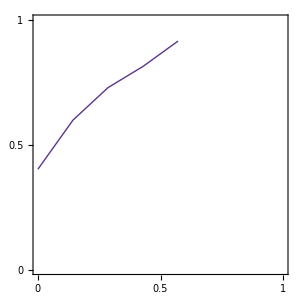

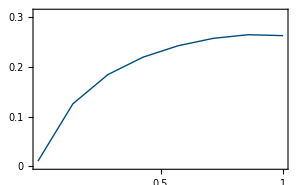

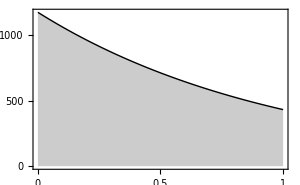

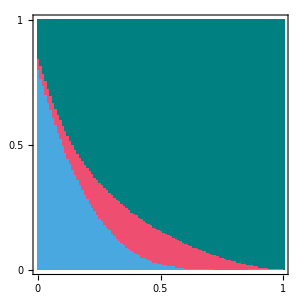

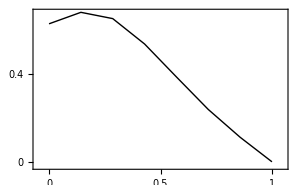

```mathematica
(*Load data*)
Get[folderdata<>"/data_fig2"];

(*Testing for stabilizing vs.disruptive selection*)
CheckSelStab[LuFig2,paramsFig2] 

(*Make plot*)
{pφ,pk,pl}=PlotEq[LuFig2,paramsFig2,1];
pSched = PlotAllocSched[LuFig2];

da=1/(Length[LuFig2]-1);
k0Num=k0/.paramsDefaultApp;
n0Num=n0/.paramsDefaultApp;
listk=Table[k0Num,{a,Range[0,1,da]}];
listn=Table[n0Num,{a,Range[0,1,da]}];

{neq,Lk,Lλ}=GetCostatekDyn[listk,listn,LuFig2,paramsFig2];
(*Age gap between two different age classes*)
Index[a_]:=IntegerPart[a/da+1];
Lλplot=Table[{a,Lλ[[Index[a]]]},{a,Range[0,1,da]}];
pλ=ListLinePlot[Lλplot,PlotStyle->{Directive[Thick,Black]},Frame->{{True, False},{True, False}},LabelStyle->style, FrameStyle->Thickness[0.007],ImageSize->300,PlotRange->{{-0.05,1.05},{-0.02,All}}];

pφ=Show[pφ,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}}, PlotRange->{{0,1},{0,1}},LabelStyle->style,AspectRatio->1]
pk=Show[pk,FrameTicks->{{{0,0.1,0.2,0.3},None},{{0.5,1},None}}, PlotRange->{{0,1},{0,0.31}},LabelStyle->style]
pl=Show[pl,FrameTicks->{{{0,500,1000},None},{{0,0.5,1},None}}, PlotRange->{{0,1},{0,All}},LabelStyle->style]
pSched=Show[pSched,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}},LabelStyle->style2]
pλ = Show[pλ,FrameTicks->{{{0,0.2,0.4,0.6,0.8},None},{{0,0.5,1},None}},LabelStyle->style]

Export[currentDirectory<>"figures/fig_2_a.pdf",pSched,Background->None];
Export[currentDirectory<>"figures/fig_2_b.pdf",pφ,Background->None];
Export[currentDirectory<>"figures/fig_2_c.pdf",pk,Background->None];
Export[currentDirectory<>"figures/fig_2_d.pdf",pl,Background->None];
Export[currentDirectory<>"figures/fig_C_1.pdf",pλ,Background->None];
```

### Figure 3 ‘learning from peers’

```mathematica
LuFig3P=IterateSeveralGen[Lu0,paramsFig3P, 50000,0.005];

file=folderdata<>"/data_Fig3P";
If[FileExistsQ[file],DeleteFile[file]]
Save[file,{LuFig3P,paramsFig3P}];
```

3167 iterations

-0.00425979

Selection is stabilizing

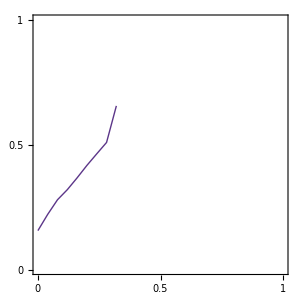

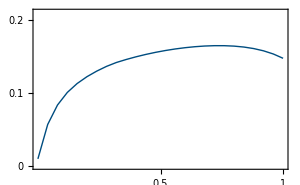

```mathematica
Get[folderdata<>"/data_Fig3P"];

CheckSelStab[LuFig3P,paramsFig3P]

{pφ,pk,pl}=PlotEq[LuFig3P,paramsFig3P,1];
pSched= PlotAllocSched[LuFig3P];

da=1/(Length[LuFig3P]-1);

k0Num=k0/.paramsFig3P;
n0Num=n0/.paramsFig3P;
listk=Table[k0Num,{a,Range[0,1,da]}];
listn=Table[n0Num,{a,Range[0,1,da]}];

{neq,Lk,Lλ}=GetCostatekDyn[listk,listn,LuFig3P,paramsFig3P];
(*Age gap between two different age classes*)
Index[a_]:=IntegerPart[a/da+1];
Lλ=Table[{a,Lλ[[Index[a]]]},{a,Range[0,1,da]}];
pλ=ListLinePlot[Lλ,PlotStyle->{Directive[Thick,Black]},Frame->{{True, False},{True, False}},LabelStyle->style, FrameStyle->Directive[Thickness[0.007],Darker[Ngrey]],FrameTicksStyle->Darker[Ngrey],ImageSize->300,PlotRange->{{-0.05,1.05},{-0.02,All}}];

pφ=Show[pφ,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}}, PlotRange->{{0,1},{0,1}},LabelStyle->style,AspectRatio->1]
pk=Show[pk,FrameTicks->{{{0,0.1,0.2},None},{{0.5,1},None}}, PlotRange->{{0,1},{0,0.21}},LabelStyle->style]

Export[currentDirectory<>"figures/fig_3_a.pdf",pφ,Background->None];
Export[currentDirectory<>"figures/fig_3_c.pdf",pk,Background->None];
```

### Figure 3 ‘learning from the oldest’

```mathematica
LuFig3O=IterateSeveralGen[Lu0,paramsFig3O, 50000,0.005];

file=folderdata<>"/data_Fig3O";
If[FileExistsQ[file],DeleteFile[file]]
Save[file,{LuFig3O,paramsFig3O}];
```

2002 iterations

-0.00255293

Selection is stabilizing

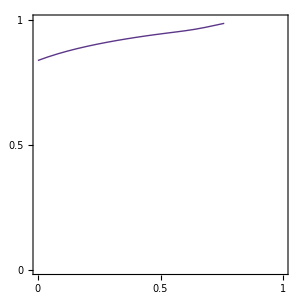

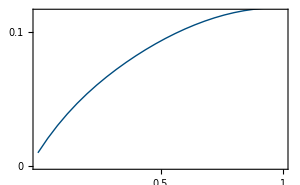

```mathematica
Get[folderdata<>"/data_Fig3O"];

CheckSelStab[LuFig3O,paramsFig3O]

{pφ,pk,pl}=PlotEq[LuFig3O,paramsFig3O,1];

pφ=Show[pφ,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}}, PlotRange->{{0,1},{0,1}},LabelStyle->style,AspectRatio->1]
pk=Show[pk,FrameTicks->{{{0,0.1,0.2},None},{{0.5,1},None}}, PlotRange->{{0,1},{0,0.115}},LabelStyle->style]

Export[currentDirectory<>"figures/fig_3_b.pdf",pφ,Background->None];
Export[currentDirectory<>"figures/fig_3_d.pdf",pk,Background->None];
```

### Figure Appendix

#### Default

```mathematica
LuDefaultApp=IterateSeveralGen[Lu0,paramsDefaultApp, 50000,0.005];

file=folderdata<>"/data_default";
If[FileExistsQ[file],DeleteFile[file]]
Save[file,{LuDefaultApp,paramsDefaultApp}];
```

2536 iterations

### Figure S1 (μ)

#### Treatment

```mathematica
paramsTreatment=Join[DropParam[paramsDefaultApp,μ],{μ->0.5}];
LuTreatment=IterateSeveralGen[Lu0,paramsTreatment, 50000,0.005];

file=folderdata<>"/data_μ";
If[FileExistsQ[file],DeleteFile[file]]
Save[file,{LuTreatment,paramsTreatment}];
```

2637 iterations

#### plot

-0.000916353

Selection is stabilizing

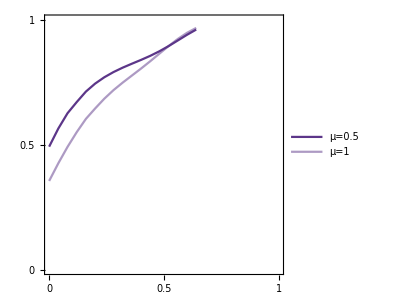

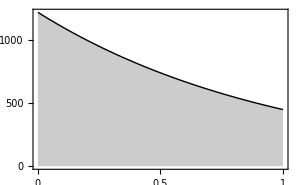

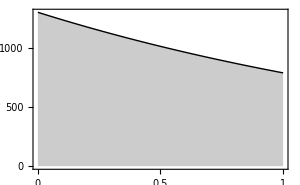

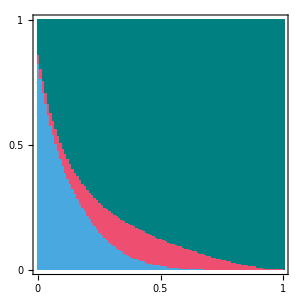

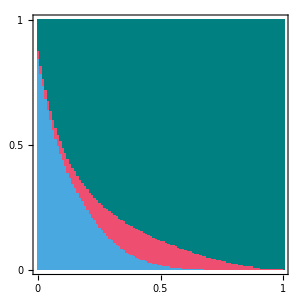

```mathematica
Get[folderdata<>"/data_default"];Get[folderdata<>"/data_μ"];

CheckSelStab[LuTreatment,paramsTreatment]

{pφ, pk}=PlotEqCompare[LuTreatment,LuDefaultApp,paramsTreatment,paramsDefaultApp,"μ=0.5","μ=1"];

{pφDefault,pkDefault,pnDefault}=PlotEq[LuDefaultApp,paramsDefaultApp,1];
{pφTreatment,pkTreatment,pnTreatment}=PlotEq[LuTreatment,paramsTreatment,1];

pSchedDefault = PlotAllocSched[LuDefaultApp];
pSchedTreatment = PlotAllocSched[LuTreatment];

pφ=Show[pφ,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}}, PlotRange->{{0,1},{0,1}},LabelStyle->style,AspectRatio->1]
pnDefault=Show[pnDefault,FrameTicks->{{{0,500, 1000, 1500},None},{{0,0.5,1},None}}, PlotRange->{{0,1},{0,All}},LabelStyle->style]
pnTreatment=Show[pnTreatment,FrameTicks->{{{0,500, 1000, 1500},None},{{0,0.5,1},None}}, PlotRange->{{0,1},{0,All}},LabelStyle->style]
pSchedDefault=Show[pSchedDefault,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}},LabelStyle->style2]
pSchedTreatment=Show[pSchedTreatment,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}},LabelStyle->style2]

Export[currentDirectory<>"figures/fig_S1_a.pdf",pφ,Background->None];
Export[currentDirectory<>"figures/fig_S1_b.pdf",pnDefault,Background->None];
Export[currentDirectory<>"figures/fig_S1_c.pdf",pnTreatment,Background->None];
Export[currentDirectory<>"figures/fig_S1_d.pdf",pSchedDefault,Background->None];
Export[currentDirectory<>"figures/fig_S1_e.pdf",pSchedTreatment,Background->None];
```

### Figure S2 (ρ)

#### Treatment

```mathematica
paramsTreatment=Join[DropParam[paramsDefaultApp,ρ],{ρ->1}];
LuTreatment=IterateSeveralGen[Lu0,paramsTreatment, 50000,0.005];

file=folderdata<>"/data_ρ";
If[FileExistsQ[file],DeleteFile[file]]
Save[file,{LuTreatment,paramsTreatment}];
```

2682 iterations

#### plot

-0.000670146

Selection is stabilizing

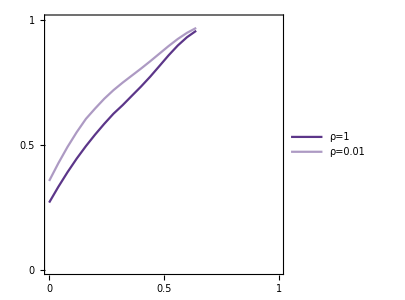

-Graphics-

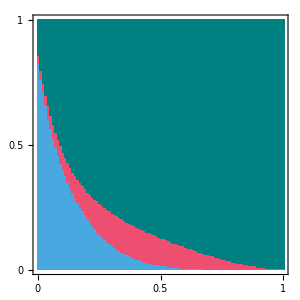

```mathematica
Get[folderdata<>"/data_default"];Get[folderdata<>"/data_ρ"];

CheckSelStab[LuTreatment,paramsTreatment]

{pφ, pk}=PlotEqCompare[LuTreatment,LuDefaultApp,paramsTreatment,paramsDefaultApp,"ρ=1","ρ=0.01"];


pSchedDefault = PlotAllocSched[LuDefaultApp];
pSchedTreatment = PlotAllocSched[LuTreatment];

pφ=Show[pφ,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}}, PlotRange->{{0,1},{0,1}},LabelStyle->style,AspectRatio->1]
pSchedDefault=Show[pSchedDefault,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}},LabelStyle->style2]
pSchedTreatment=Show[pSchedTreatment,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}},LabelStyle->style2]

Export[currentDirectory<>"figures/fig_S2_a.pdf",pφ,Background->None];
Export[currentDirectory<>"figures/fig_S2_b.pdf",pSchedDefault,Background->None];
Export[currentDirectory<>"figures/fig_S2_c.pdf",pSchedTreatment,Background->None];
```

### Figure S3 (ξ)

#### Treatment

```mathematica
paramsTreatment=Join[DropParam[paramsDefaultApp,ξ],{ξ->0.1}];
LuTreatment=IterateSeveralGen[Lu0,paramsTreatment, 50000,0.005];

file=folderdata<>"/data_ξ";
If[FileExistsQ[file],DeleteFile[file]]
Save[file,{LuTreatment,paramsTreatment}];
```

1719 iterations

#### plot

-0.000562919

Selection is stabilizing

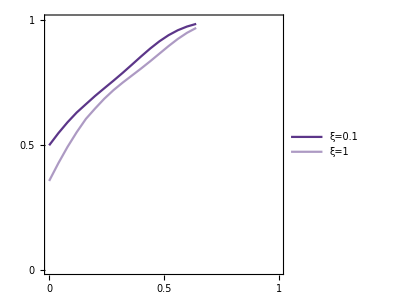

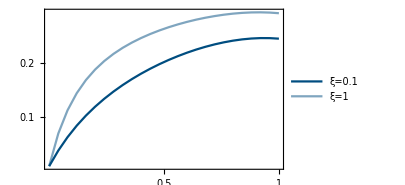

-Graphics-

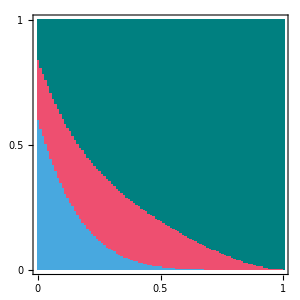

```mathematica
Get[folderdata<>"/data_default"];Get[folderdata<>"/data_ξ"];

CheckSelStab[LuTreatment,paramsTreatment]

{pφ, pk}=PlotEqCompare[LuTreatment,LuDefaultApp,paramsTreatment,paramsDefaultApp,"ξ=0.1","ξ=1"];
{pφDefault,pkDefault,pnDefault}=PlotEq[LuDefaultApp,paramsDefaultApp,1];
{pφTreatment,pkTreatment,pnTreatment}=PlotEq[LuTreatment,paramsTreatment,1];
pSchedDefault = PlotAllocSched[LuDefaultApp];
pSchedTreatment = PlotAllocSched[LuTreatment];

pφ=Show[pφ,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}}, PlotRange->{{0,1},{0,1}},LabelStyle->style,AspectRatio->1]
pk=Show[pk,FrameTicks->{{{0,0.1,0.2,0.3},None},{{0.5,1},None}}, PlotRange->{{0,1},{0,All}},LabelStyle->style]
pkDefault=Show[pkDefault,FrameTicks->{{{0,0.1,0.2},None},{{0.5,1},None}}, PlotRange->{{0,1},{0,All}},LabelStyle->style];
pkTreatment=Show[pkTreatment,FrameTicks->{{{0,0.1,0.2},None},{{0.5,1},None}}, PlotRange->{{0,1},{0,All}},LabelStyle->style];
pSchedDefault=Show[pSchedDefault,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}},LabelStyle->style2]
pSchedTreatment=Show[pSchedTreatment,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}},LabelStyle->style2]

Export[currentDirectory<>"figures/fig_S3_a.pdf",pφ,Background->None];
Export[currentDirectory<>"figures/fig_S3_b.pdf",pk,Background->None];
Export[currentDirectory<>"figures/fig_S3_c.pdf",pSchedDefault,Background->None];
Export[currentDirectory<>"figures/fig_S3_d.pdf",pSchedTreatment,Background->None];
```

### Figure S4 (ϵ)

#### Treatment

```mathematica
paramsTreatment=Join[DropParam[paramsDefaultApp,ϵ],{ϵ->1}];
LuTreatment=IterateSeveralGen[Lu0,paramsTreatment, 50000,0.005];

file=folderdata<>"/data_ϵ";
If[FileExistsQ[file],DeleteFile[file]]
Save[file,{LuTreatment,paramsTreatment}];
```

1527 iterations

#### plot

-0.0128548

Selection is stabilizing

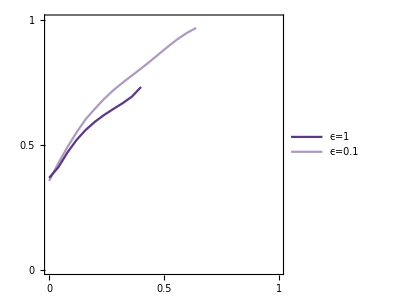

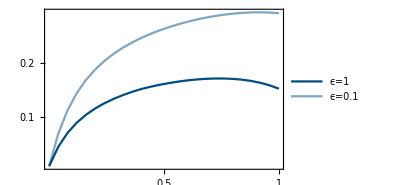

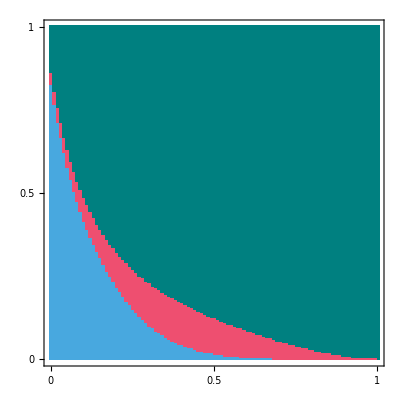

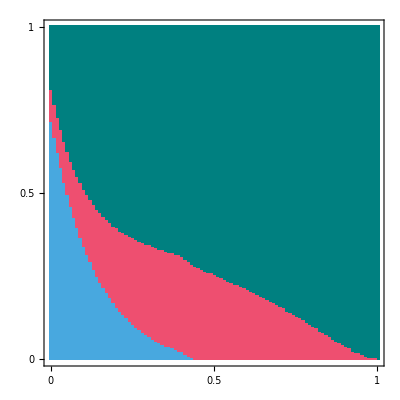

```mathematica
Get[folderdata<>"/data_default"];Get[folderdata<>"/data_ϵ"];

CheckSelStab[LuTreatment,paramsTreatment]

{pφ, pk}=PlotEqCompare[LuTreatment,LuDefaultApp,paramsTreatment,paramsDefaultApp,"ϵ=1","ϵ=0.1"];
pSchedDefault = PlotAllocSched[LuDefaultApp];
pSchedTreatment = PlotAllocSched[LuTreatment];

pφ=Show[pφ,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}}, PlotRange->{{0,1},{0,1}},LabelStyle->style,AspectRatio->1]
pk=Show[pk,FrameTicks->{{{0,0.1,0.2, 0.3},None},{{0.5,1},None}}, PlotRange->{{0,1},{0,All}},LabelStyle->style]
pSchedDefault=Show[pSchedDefault,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}},LabelStyle->style2]
pSchedTreatment=Show[pSchedTreatment,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}},LabelStyle->style2]

Export[currentDirectory<>"figures/fig_S4_a.pdf",pφ,Background->None];
Export[currentDirectory<>"figures/fig_S4_b.pdf",pk,Background->None];
Export[currentDirectory<>"figures/fig_S4_c.pdf",pSchedDefault,Background->None];
Export[currentDirectory<>"figures/fig_S4_d.pdf",pSchedTreatment,Background->None];
```

### Figure S5 (α)

#### Treatment

```mathematica
paramsTreatment=Join[DropParam[paramsDefaultApp,α],{α->0.05}];
LuTreatment=IterateSeveralGen[Lu0,paramsTreatment, 50000,0.005];

file=folderdata<>"/data_α";
If[FileExistsQ[file],DeleteFile[file]]
Save[file,{LuTreatment,paramsTreatment}];
```

2999 iterations

#### plot

-0.000441048

Selection is stabilizing

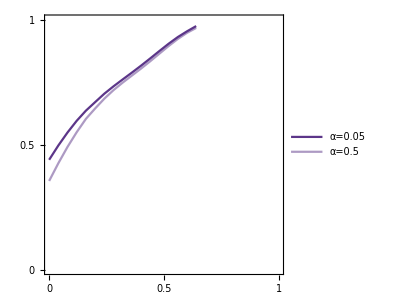

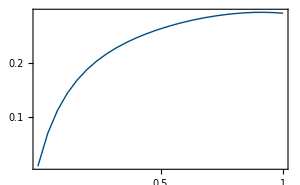

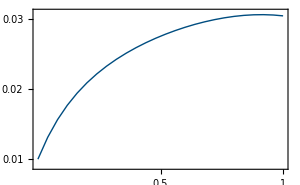

```mathematica
Get[folderdata<>"/data_default"];Get[folderdata<>"/data_α"];

CheckSelStab[LuTreatment,paramsTreatment]

{pφ, pk}=PlotEqCompare[LuTreatment,LuDefaultApp,paramsTreatment,paramsDefaultApp,"α=0.05","α=0.5"];
{pφDefault,pkDefault,pnDefault}=PlotEq[LuDefaultApp,paramsDefaultApp,1];
{pφTreatment,pkTreatment,pnTreatment}=PlotEq[LuTreatment,paramsTreatment,1];


pφ=Show[pφ,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}}, PlotRange->{{0,1},{0,1}},LabelStyle->style,AspectRatio->1]
pkDefault=Show[pkDefault,FrameTicks->{{{0,0.1,0.2,0.3},None},{{0.5,1},None}}, PlotRange->{{0,1},{0,All}},LabelStyle->style]
pkTreatment=Show[pkTreatment,FrameTicks->{{{0,0.01,0.02,0.03},None},{{0.5,1},None}}, PlotRange->{{0,1},{0.009,0.031}},LabelStyle->style]

Export[currentDirectory<>"figures/fig_S5_a.pdf",pφ,Background->None];
Export[currentDirectory<>"figures/fig_S5_b.pdf",pkDefault,Background->None];
Export[currentDirectory<>"figures/fig_S5_c.pdf",pkTreatment,Background->None];
```

### Figure S6 (β)

#### Treatment

```mathematica
paramsTreatment=Join[DropParam[paramsDefaultApp,β],{β->0.06}];
LuTreatment=IterateSeveralGen[Lu0,paramsTreatment, 50000,0.005];

file=folderdata<>"/data_β";
If[FileExistsQ[file],DeleteFile[file]]
Save[file,{LuTreatment,paramsTreatment}];
```

2538 iterations

#### plot

-0.000803923

Selection is stabilizing

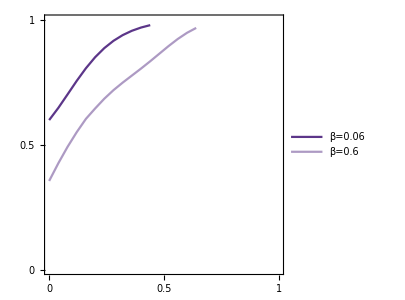

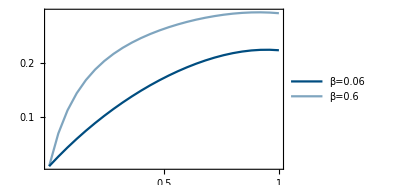

```mathematica
Get[folderdata<>"/data_default"];Get[folderdata<>"/data_β"];

CheckSelStab[LuTreatment,paramsTreatment]

{pφ, pk}=PlotEqCompare[LuTreatment,LuDefaultApp,paramsTreatment,paramsDefaultApp,"β=0.06","β=0.6"];

pφ=Show[pφ,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}}, PlotRange->{{0,1},{0,1}},LabelStyle->style,AspectRatio->1]
pk=Show[pk,FrameTicks->{{{0,0.1,0.2, 0.3},None},{{0.5,1},None}}, PlotRange->{{0,1},{0,All}},LabelStyle->style]

Export[currentDirectory<>"figures/fig_S6_a.pdf",pφ,Background->None];
Export[currentDirectory<>"figures/fig_S6_b.pdf",pk,Background->None];
```

### Figure S7 (K)

#### Treatment

```mathematica
paramsTreatment=Join[DropParam[paramsDefaultApp,K],{K->0.1}];
LuTreatment=IterateSeveralGen[Lu0,paramsTreatment, 50000,0.005];

file=folderdata<>"/data_K";
If[FileExistsQ[file],DeleteFile[file]]
Save[file,{LuTreatment,paramsTreatment}];
```

2925 iterations

#### plot

-0.000348784

Selection is stabilizing

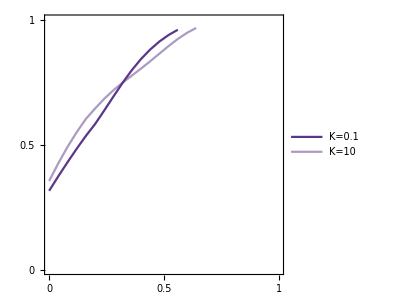

-Graphics-

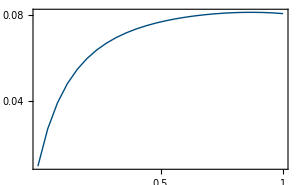

```mathematica
Get[folderdata<>"/data_default"];Get[folderdata<>"/data_K"];

CheckSelStab[LuTreatment,paramsTreatment]

{pφ, pk}=PlotEqCompare[LuTreatment,LuDefaultApp,paramsTreatment,paramsDefaultApp,"K=0.1","K=10"];
{pφDefault,pkDefault,pnDefault}=PlotEq[LuDefaultApp,paramsDefaultApp,1];
{pφTreatment,pkTreatment,pnTreatment}=PlotEq[LuTreatment,paramsTreatment,1];


pφ=Show[pφ,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1},None}}, PlotRange->{{0,1},{0,1}},LabelStyle->style,AspectRatio->1]
pkDefault=Show[pkDefault,FrameTicks->{{{0,0.1,0.2,0.3},None},{{0.5,1},None}}, PlotRange->{{0,1},{0,All}},LabelStyle->style]
pkTreatment=Show[pkTreatment,FrameTicks->{{{0,0.04, 0.08},None},{{0.5,1},None}}, PlotRange->{{0,1},{0,All}},LabelStyle->style]

Export[currentDirectory<>"figures/fig_S7_a.pdf",pφ,Background->None];
Export[currentDirectory<>"figures/fig_S7_b.pdf",pkDefault,Background->None];
Export[currentDirectory<>"figures/fig_S7_c.pdf",pkTreatment,Background->None];
```